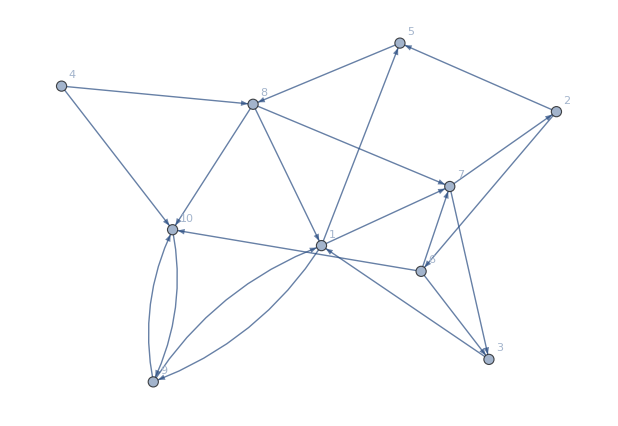

```mathematica
randomGraph=RandomGraph[{10,20},DirectedEdges->True,VertexLabels->Automatic]
```

```mathematica
VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]
```

{2,3,5,7,8,10}

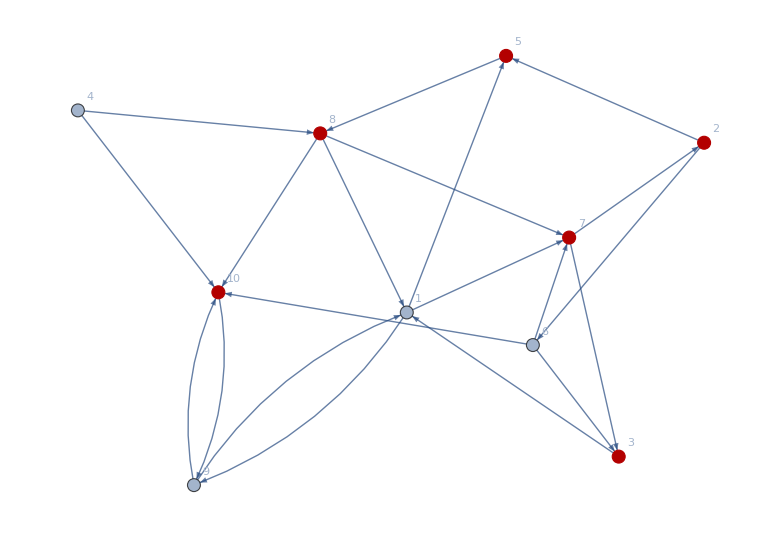

```mathematica
HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]
```

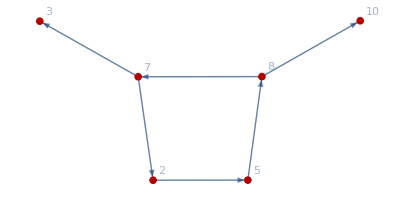

```mathematica
Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]
```

```mathematica
FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]
```

{2->5,7->3,8->10}

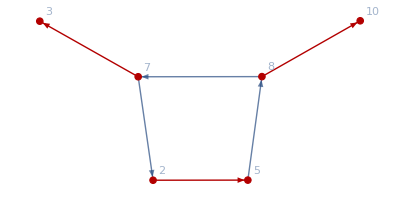

```mathematica
HighlightGraph[Graph[{2,3,5,7,8,10},{SparseArray[Automatic,{6,6},0,{1,{{0,1,1,2,4,6,6},{{3},{5},{1},{2},{4},{6}}},Pattern}],Null},{VertexLabels->{Automatic},GraphHighlight->{10,5,2,7,8,3}}],{2->5,7->3,8->10}]
```

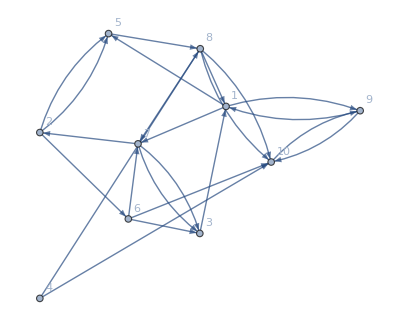

```mathematica
EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]
```

```mathematica
EulerianGraphQ[EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]]
```

False

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

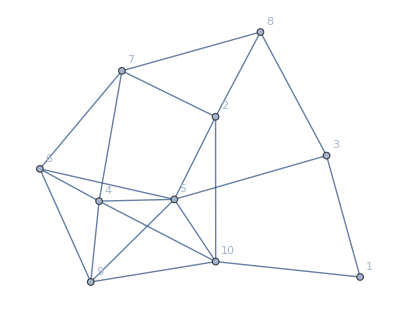

```mathematica
randomGraph=RandomWeightedMixedGraph[{10,20},0,RandomInteger[{1,3}]&,VertexLabels->Automatic]
```

```mathematica
EulerianGraphQ[EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]]
```

True

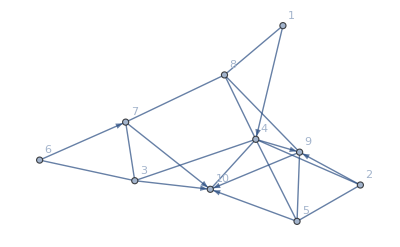

```mathematica
randomMixedGraph=RandomWeightedMixedGraph[{10,20},0.6,RandomInteger[{1,3}]&,VertexLabels->Automatic]
```

```mathematica
VertexDegree[randomMixedGraph]
```

{2,3,4,5,4,2,2,3,2,1}

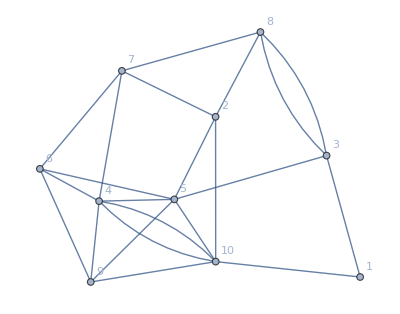

```mathematica
EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]
```

```mathematica
VertexDegree[EdgeAdd[randomGraph,FindEdgeCover[Subgraph[HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]],VertexList[randomGraph,x_/;OddQ@VertexDegree[randomGraph,x]]]]]]
```

{2,4,4,6,6,4,4,4,4,6}

```mathematica
EdgeList[randomMixedGraph,_<->_]
```

{1<->8,2<->5,3<->4,3<->6,4<->5,4<->10,7<->8,8<->9}

```mathematica
EdgeList[randomMixedGraph,_<->_]/.{u_<->v_:>RandomChoice[{u->v,v->u}]}
```

{1->8,2->5,3->4,6->3,4->5,10->4,8->7,8->9}

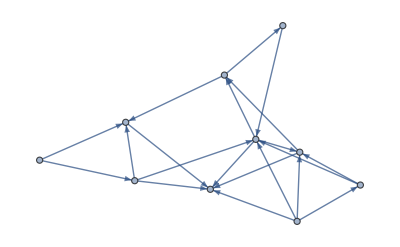

```mathematica
Graph[Join[EdgeList[randomMixedGraph,_DirectedEdge],EdgeList[randomMixedGraph,_<->_]/.{u_<->v_:>RandomChoice[{u->v,v->u}]}]]
```

```mathematica
?FindMinimumCostFlow
```

```mathematica
A1=EdgeList[randomMixedGraph,_<->_]/.{u_<->v_:>RandomChoice[{u->v,v->u}]}
```

{8->1,2->5,3->4,3->6,4->5,10->4,8->7,8->9}

```mathematica
A2=EdgeList@ReverseGraph[A1]
```

{1->8,5->2,5->4,4->3,4->10,6->3,7->8,9->8}

```mathematica
Names["*Reverse*"]
```

{AllowReverseGroupClose,AudioReverse,BioSequenceReverseComplement,DataReversed,DegreeReverseLexicographic,IntegerReverse,NotReverseElement,Reverse,ReverseApplied,ReverseBiorthogonalSplineWavelet,ReverseElement,ReverseEquilibrium,ReverseGraph,ReverseSort,ReverseSortBy,ReverseUpEquilibrium,SequenceReverseLayer,StringReverse}

```mathematica
Graph[{1<->2,1<->2,1<->2,1<->2},EdgeWeight->Thread[{1<->2,1<->2,1<->2,1<->2}->Range[4]]]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,1<->2,1<->2,1<->2},EdgeWeight->Thread[{1<->2,1<->2,1<->2,1<->2}->Range[4]]]]//MatrixForm
```

(0 | 4
4 | 0)

```mathematica
EdgeTaggedGraph[{Style[1<->2,Red],Style[1<->2,Blue],2<->3,3<->1}]
```

-Graphics-

```mathematica
EdgeTaggedGraph[{UndirectedEdge[1,2,a],UndirectedEdge[1,2,b]},EdgeWeight->Thread[{UndirectedEdge[1,2,a],UndirectedEdge[1,2,b]}->{1,2}]]
```

-Graphics-

```mathematica
AnnotationValue[{EdgeTaggedGraph[{UndirectedEdge[1,2,a],UndirectedEdge[1,2,b]},EdgeWeight->Thread[{UndirectedEdge[1,2,a],UndirectedEdge[1,2,b]}->{1,2}]],UndirectedEdge[1,2,a]},EdgeWeight]
```

1

```mathematica
EdgeList[randomMixedGraph,_UndirectedEdge]
```

{1<->8,2<->5,3<->4,3<->6,4<->5,4<->10,7<->8,8<->9}

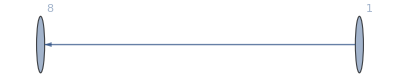

```mathematica
EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic]&/@{1<->8}
```

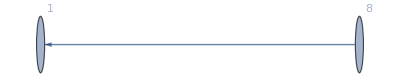

```mathematica
EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic]&/@{1<->8}
```

```mathematica
EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{0}],VertexLabels->Automatic]&/@{1<->8}
```

{-Graphics-}

```mathematica
GraphSum[Graph[{1<->8},EdgeWeight->{1<->8->AnnotationValue[{randomMixedGraph,1<->8},EdgeWeight]}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic]&[1<->8],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic]&[1<->8],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{0}],VertexLabels->Automatic]&[1<->8]]
```

-Graphics-

AnnotationValue::pvobj: {} is not an object with annotations.

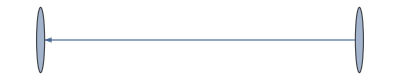
AnnotationValue[{{-Graphics-},18a1},EdgeWeight]

```mathematica
AnnotationValue[{EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}]]&/@{1<->8},DirectedEdge[First[#],Last[#],a1]&[1<->8]},EdgeWeight]
```

```mathematica
AnnotationValue[{First[EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}]]&/@{1<->8}],DirectedEdge[First[#],Last[#],a1]&[1<->8]},EdgeWeight]
```

1

```mathematica
GraphSum[Graph[{1<->8},EdgeWeight->{1<->8->AnnotationValue[{randomMixedGraph,1<->8},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{UndirectedEdge[1,2,a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[1<->8],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{UndirectedEdge[1,2,a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[1<->8],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&[1<->8]]
```

-Graphics-

```mathematica
GraphSum@@Random
```

GraphSum::graph: A graph object is expected at position 4 in ….

General::stop: Further output of GraphSum::graph will be suppressed during this calculation.


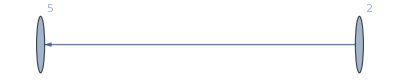
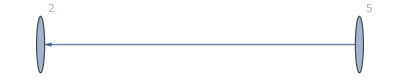
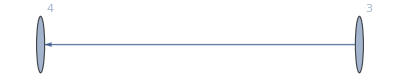
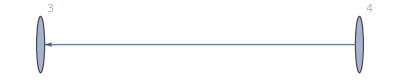
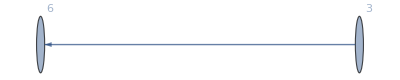
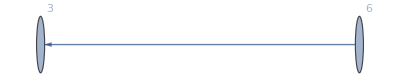
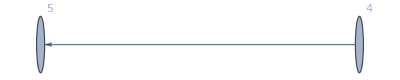
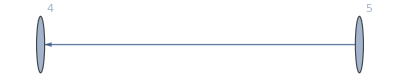
{GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (1<->8)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (2<->5)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (3<->4)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (3<->6)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (4<->5)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (4<->10)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (7<->8)],GraphSum[-Graphics-,-Graphics-,-Graphics-,EdgeTaggedGraph[{First[#1]Last[#1]a3},EdgeWeight→Thread[{12a3}→{0}],VertexLabels→Automatic,EdgeCapacity→{2}]& (8<->9)]}

```mathematica
(edge↦GraphSum[Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{DirectedEdge[First[#],Last[#],a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{DirectedEdge[Last[#],First[#],a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&edge])/@EdgeList[randomMixedGraph,_UndirectedEdge]
```

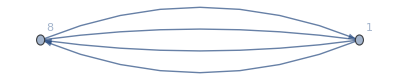
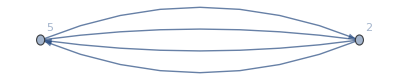
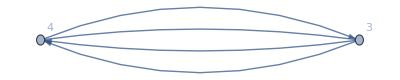
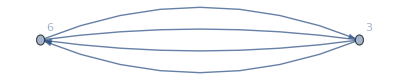
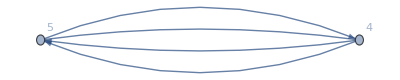
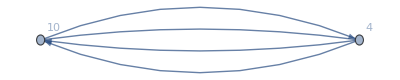
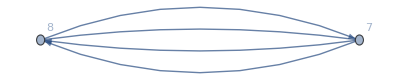
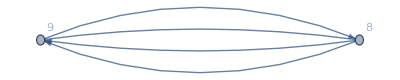

```mathematica
(edge↦GraphSum[Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{DirectedEdge[First[#],Last[#],a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{DirectedEdge[Last[#],First[#],a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&[edge],VertexLabels->Automatic])/@EdgeList[randomMixedGraph,_UndirectedEdge]
```

```mathematica
GraphSum@@((edge↦GraphSum[Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{DirectedEdge[First[#],Last[#],a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{DirectedEdge[Last[#],First[#],a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&[edge],VertexLabels->Automatic])/@EdgeList[randomMixedGraph,_UndirectedEdge])
```

-Graphics-

```mathematica
GraphSum[GraphSum@@((edge↦GraphSum[Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{DirectedEdge[First[#],Last[#],a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{DirectedEdge[Last[#],First[#],a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&[edge],VertexLabels->Automatic])/@EdgeList[randomMixedGraph,_UndirectedEdge]),GraphSum@@((edge↦Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}])/@EdgeList[randomMixedGraph,_DirectedEdge])]
```

-Graphics-

```mathematica
ℱ=FindMinimumCostFlow[-Graphics-,1,8,"OptimumFlowData"]
```

OptimumFlowData[…]

```mathematica
ℱ["Properties"]
```

{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList}

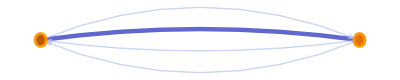
<|CostValue→3,EdgeList→{1<->8},FlowGraph→-Graphics-,FlowMatrix→SparseArray[…],FlowTable→OptimumFlowData[…][FlowTable],FlowValue→0,Properties→{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList},ResidualGraph→OptimumFlowData[…][ResidualGraph],VertexList→{1,8}|>

```mathematica
AssociationMap[ℱ[#]&,ℱ["Properties"]]
```

```mathematica
ℱ=FindMinimumCostFlow[GraphSum[GraphSum@@((edge↦GraphSum[Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a1]},EdgeWeight->Thread[{DirectedEdge[First[#],Last[#],a1]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[Last[#],First[#],a2]},EdgeWeight->Thread[{DirectedEdge[Last[#],First[#],a2]}->{AnnotationValue[{randomMixedGraph,#},EdgeWeight]}],VertexLabels->Automatic,EdgeCapacity->{Infinity}]&[edge],EdgeTaggedGraph[{DirectedEdge[First[#],Last[#],a3]},EdgeWeight->Thread[{UndirectedEdge[1,2,a3]}->{0}],VertexLabels->Automatic,EdgeCapacity->{2}]&[edge],VertexLabels->Automatic])/@EdgeList[randomMixedGraph,_UndirectedEdge]),GraphSum@@((edge↦Graph[{edge},EdgeWeight->{edge->AnnotationValue[{randomMixedGraph,edge},EdgeWeight]},EdgeCapacity->{Infinity}])/@EdgeList[randomMixedGraph,_DirectedEdge])],1,2,"OptimumFlowData"]
```

OptimumFlowData[…]